# Specialne funkcije - Ortogonalnost

## Legendrovi polinomi P_n(x)

Legendrova diferencialna enačba:
(x^2-1)y''+2xy'-n(n+1)y=0

Ena rešitev zgornje Legendrove diferencialne enačbe je polinom
               P_n(x) =∑_(k=0)^N (-1)^k((2 n-2 k)!)/(2^n k! (n-k)! (n-2 k)!)x^(n-2 k),          kjer je  N=Floor[n/2]
V Mathematici ga zapišemo LegendreP[n,x].

### Ortogonalnost Legendrovih polinomov

Legendrovi polinomi so ortogonalni brez uteži (utež je 1)  na intervalu (-1,1), to pomeni, da za n≠m velja
            ∫_-1^1 P_n(x)P_m(x)ⅆx = 0
            
            Ortogonalnost pomeni skalarni produkt, dveh različnih je = 0

```mathematica
(*Izberemo dva random indeksa in eden je manjši da je različen*)

n=RandomInteger[{1,20}]
m=RandomInteger[{0,n-1}]
Integrate[LegendreP[n,x]LegendreP[m,x],{x,-1,1}]
```

8

4

0

POMNI!
Poljubno funkcijo f(x) se da razviti po Legendrovih polinomih na sledeč način:
               f (x)=∑_(n=0)^∞ C_n P_n(x) ,     kjer je     C_n=1/(||P_n(||)^2)∫_-1^1 f(x)P_n(x)ⅆx,     ||P_n(||)^2=∫_-1^1 P_n^2(x)ⅆx   norma

```mathematica
Clear[n]
Integrate[LegendreP[n,x]^2,{x,-1,1}, Assumptions->{n ∈ Integers, n>-1} ] // FullSimplify

Table[Integrate[LegendreP[n,x]^2,{x,-1,1}], {n,0,10}] 
Table[2/(2n+1),{n,0,10}]
```

Integrate[LegendreP[n,x]^2,{x,-1,1},Assumptions→n∈ℤ&&n>-1]

{2,2/3,2/5,2/7,2/9,2/11,2/13,2/15,2/17,2/19,2/21}

{2,2/3,2/5,2/7,2/9,2/11,2/13,2/15,2/17,2/19,2/21}

## Besselove funkcije

Besselova diferencialna enačba
x^2 y''+x y'+(x^2-ν^2)y=0

Ena rešitev zgornje Beselove diferencialne enačbe je Besselova funkcija prve vrste reda ν:
               J_ν(x) =∑_(k=0)^∞ (-1)^k/(k! Γ(ν+k+1))(x/2)^(ν+2 k) 
V Mathematici jo zapišemo BesselJ[v,x].

### Ortogonalnost Besselovih funkcij

Za fiksen n sestavljajo Besselove funkcije prve vrste J_n(α_mn/R x), kjer m = 1, 2, 3 ..., ortogonalen sistem funkcij na intervalu (0,R) z utežjo p(x) = x, kjer je α_mn m-ta ničla funkcije J_n(x).

Teh ortogonalnih sistemov je neskončno mnogo; za vsak n eden.

1. S pomočjo spodnje rešitve preverite zgoraj opisano ortogonalnost
      Besselovih funkcij in izračunajte njihove norme, tj. izračunajte integrale

               ∫_0^R x J_n(α_jn/R x) J_n(α_kn/R x) ⅆx,     če j≠k    jta in kta ničla

               (‖J_n(α_mn/R x) ‖)^2 = ∫_0^R x J_n^2 (α_mn/R x) ⅆx

Rezultata: 0, R^2/2(J_(n+1))^2 (α_mn)

```mathematica
k=137;
Sin[k π]
BesselJ[0,BesselJZero[0,k]]
Clear[k]
Sin[k π]
BesselJ[0,BesselJZero[0,k]] (* matematika ne ve da hočemo cela števila*)
```

0

0

Sin[k π]

BesselJ[0,BesselJZero[0,k]]

```mathematica
Simplify[Sin[k π],Assumptions->k∈Integers]
FullSimplify[BesselJ[0,BesselJZero[0,k]],Assumptions->{k∈Integers,k>0}]
FullSimplify[BesselJ[0,BesselJZero[0,k]],Assumptions->{k∈PositiveIntegers}]
```

0

0

0

```mathematica
Clear[R,n,m]
gj[x_]:=BesselJ[n,BesselJZero[n,j]/R x];(*vstavimo jto ničlo*)
gk[x_]:=BesselJ[n,BesselJZero[n,k]/R x];
Integrate[x*gj[x]*gk[x],{x,0,R},Assumptions->{n∈Integers,n>-1}]
%/.{ BesselJ[n,BesselJZero[n,j]]->0,BesselJ[n,BesselJZero[n,k]]->0}
```

-(R^2 (BesselJ[-1+n,BesselJZero[n,j]] BesselJ[n,BesselJZero[n,k]] BesselJZero[n,j]-BesselJ[-1+n,BesselJZero[n,k]] BesselJ[n,BesselJZero[n,j]] BesselJZero[n,k]))/(BesselJZero[n,j]^2-BesselJZero[n,k]^2)

0

```mathematica
Integrate[x*gj[x]*gk[x],{x,0,R},Assumptions->{n∈Integers,n>-1, j∈ PositiveIntegers,  k∈ PositiveIntegers}]//FullSimplify (*to ne dela*)
```

(R^2 (-BesselJ[-1+n,BesselJZero[n,j]] BesselJ[n,BesselJZero[n,k]] BesselJZero[n,j]+BesselJ[-1+n,BesselJZero[n,k]] BesselJ[n,BesselJZero[n,j]] BesselJZero[n,k]))/(BesselJZero[n,j]^2-BesselJZero[n,k]^2)

```mathematica
Integrate[x BesselJ[n,BesselJZero[n,m]/R x]^2,{x,0,R},Assumptions->{n∈Integers,n>-1}]/.BesselJ[n,BesselJZero[n,m]]->0
```

1/2 R^2 BesselJ[1+n,BesselJZero[n,m]]^2

Podrobneje si oglejmo ortogonalen sistem za n=0.

Vsaka ničla α_m0 določa eno funkcijo. Ortogonalen sistem tako sestavljajo funkcije
               J_0(α_10/R x), J_0(α_20/R x), J_0(α_30/R x) ...

Grafi nekaj prvih funkcij J_0(α_m0/R x) iz navedenega ortogonalnega sistema:

```mathematica
R=2;
Table[
αm0=N[BesselJZero[0,m]];
Plot[BesselJ[0,αm0/R x], {x,0,R},PlotStyle->Thick],
{m,1,6}]
```

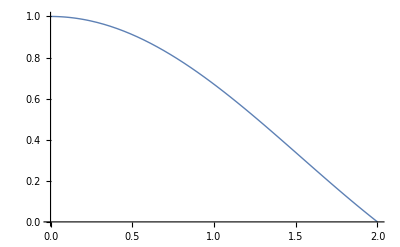
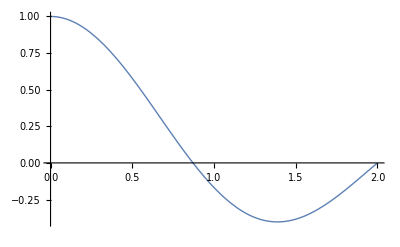
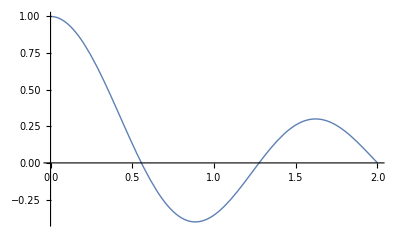
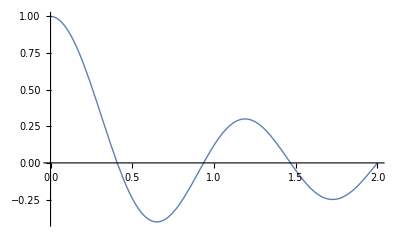
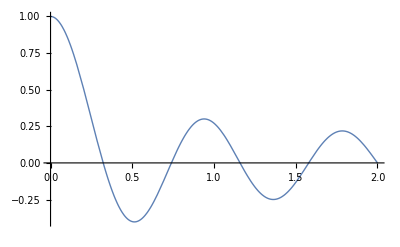
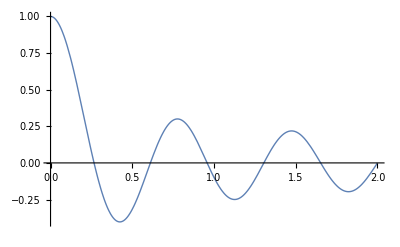
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
(*
	v 0 imajo vse enako vrednost, tako kot jo ima J_n(0),
	v R pa so vse enake 0
	najprej imamo eno ničlo na koncu potem pa ima vsaka naslednja eno ničlo več kot prejšnja.
	kajti to je vedno večja skrčitev/razteg.
	-raztegi so ravno tako nastavljeni, da pride m-ta ničla pri R.
*)
```

POMNI!
Poljubno funkcijo f(x) se da razviti po Besselovih funkcijah J_0(α_k0/R x) na intervalu 0<x<R na sledeč način:
                f(x)=∑_(k=1)^∞ C_k J_0(α_k0/R x) ,     kjer je     C_k=1/(R^2/2 J_1^2(α_k0))∫_0^R x f(x)J_0(α_k0/R x)ⅆx

### Primeri nalog za preverjanje

1. Izračunajte prve M=4 člene v razvoju funkcije
               f(x)=(2+x)(20-11x)
      po Besselovih funkcijah J_0(α_k0/2 x) na intervalu (0,2)!
      (a)  Uspešnost rešitve preverite grafično!
      (b)  Koliko je ∑_(k=1)^M c_k?

Rezultat: 42.1034

{39.0753,2.64294,-4.59777,4.98301}

{BesselJ[0,1/2 x BesselJZero[0,1]],BesselJ[0,1/2 x BesselJZero[0,2]],BesselJ[0,1/2 x BesselJZero[0,3]],BesselJ[0,1/2 x BesselJZero[0,4]]}

39.0753 BesselJ[0,1/2 x BesselJZero[0,1]]+2.64294 BesselJ[0,1/2 x BesselJZero[0,2]]-4.59777 BesselJ[0,1/2 x BesselJZero[0,3]]+4.98301 BesselJ[0,1/2 x BesselJZero[0,4]]

39.0753 BesselJ[0,1/2 x BesselJZero[0,1]]+2.64294 BesselJ[0,1/2 x BesselJZero[0,2]]-4.59777 BesselJ[0,1/2 x BesselJZero[0,3]]+4.98301 BesselJ[0,1/2 x BesselJZero[0,4]]

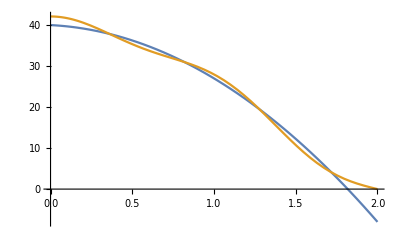

42.1034

42.1034

```mathematica
f= (2+x)(20-11 x);
(*f= (2-x)(20-11 x);*)
M=4;
R=2;
ck =Table[

1/(R^2 /2 * BesselJ[1, BesselJZero[0,k]]^2)  NIntegrate[x f BesselJ[0,N[BesselJZero[0,k]] x/R], {x,0,R}]
, {k,1,M}] //N

(*za a rabimo še pripadajoče ortogonalne funkcije, da lahko naredimo pribljižek za iskano vsoto*)

gk = Table[

BesselJ[0, BesselJZero[0,k] x/R]
, {k,1,M}]
priblizek = Sum[ck[[n]] gk[[n]], {n,1,M}]

(*lažje*)
priblizek = ck.gk

Plot[{f,priblizek},{x,0,R}]

(*B točka, ker želimo sešteti vse elemente v seznamu*)

Sum[ck[[n]],{n,1,M}]
Total[ck]
```

2. Razvijte funkcijo
               f(x)=|x-1/3|
      po Legendrovih polinomih P_n(x) ,torej f(x)=∑_(n=0)^∞ c_n P_n(x)
      (a)  Zapišite začetek vrste do vključno P_4(x) !
      (b)  Koliko je ∑_(n=0)^4 c_n?

Rezultat:
      (a)  5/9-(13 x)/27+20/81 (-1+3 x^2)+28/243 (-3 x+5 x^3)+1/243 (-3+30 x^2-35 x^4)
      (b)  0.765432

{5/9,-13/27,40/81,56/243,-8/243}

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}

5/9-(13 x)/27+20/81 (-1+3 x^2)+28/243 (-3 x+5 x^3)+1/243 (-3+30 x^2-35 x^4)

5/9+List^2-(13 x)/27+20/81 (-1+3 x^2)+28/243 (-3 x+5 x^3)

5/9-(13 x)/27+20/81 (-1+3 x^2)+28/243 (-3 x+5 x^3)+1/243 (-3+30 x^2-35 x^4)

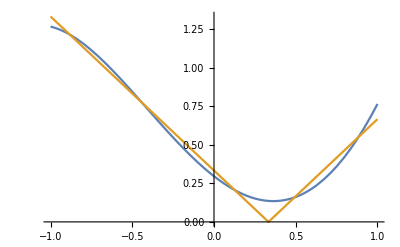

0.765432

0.765432

```mathematica
f= Abs[x - 1/3];
M=4;
cn=Table[

Integrate[f* LegendreP[n,x],{x,-1,1}]/ Integrate[LegendreP[n,x]^2,{x,-1,1}]
,{n,0,M}
]
Pn= Table[LegendreP[n,x],{n,0,M}]


priblizek=cn.Pn


Sum[cn[[n]] Pn[[n]],{n,0,M}] (*Pazi indeksi grejo od prvega naprej! P0 je prvi element*)
Sum[cn[[n]] Pn[[n]],{n,1,M+1}] 


(*Grafično*)

Plot[{priblizek,f}, {x,-1,1}]


(*točka b*)
Total[cn] //N

(*Če ne bi potrebovali vseh*)
Sum[cn[[n]],{n,1,M+1}] //N
```

3. Poiščite polinom 3.stopnje
               p(x)=x^3+a x^2+b x+c,
      ki je ortogonalen na funkcije
               f_n(x)=x^n, n=0,1,2
      na intervalu (1,3) z utežjo ρ(x)=x.
      Koliko je p(3)?

Rezultat: 0.32437

```mathematica
p= x^3 + a x^2 +b x +c;
utez=x;
Solve[
{
Integrate[p*1*utez, {x,1,3}]==0,
Integrate[p*x*utez, {x,1,3}]==0,
Integrate[p*x^2*utez, {x,1,3}]==0
},{a,b,c}]//Flatten

p/.% /.x-> 3//N
```

{a→-1461/238,b→1425/119,c→-8749/1190}

0.32437

4. Poiščite polinom 13.stopnje
               p(x)=x^13+∑_(n=0)^12 c_n x^n,
      ki je ortogonalen na funkcije
               f_n(x)=x^n, n=0,1,...,12
      na intervalu (1,3) z utežjo ρ(x)=x.
      Koliko je p(3)?

Rezultat: 0.000626003

```mathematica
(*Sedaj jih je preveč da bo ročno*)
M=13;
a=1;
b=3;
utez= x;
x0=3;

p=x^M + Sum[c[n]x^n,{n,0,M-1}]
Table[ Integrate[p*x^n * utez,{x,a,b}],{n,0,M-1}];
Solve[%==0, Table[c[n],{n,0,M-1}]]


(*ali: generiramo z table enčbe, prej smo dobili samo seznam integralov *)

Solve[Table[ Integrate[p*x^n * utez,{x,a,b}]==0,{n,0,M-1}], Table[c[n],{n,0,M-1}]] //Flatten

p/.%/.x-> x0 //N
```

x^13+c[0]+x c[1]+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]+x^6 c[6]+x^7 c[7]+x^8 c[8]+x^9 c[9]+x^10 c[10]+x^11 c[11]+x^12 c[12]

{{c[0]→-83981864256816418627/22541648189737050,c[1]→20755237039247942959/751388272991235,c[2]→-6376694496740378083/68308024817385,c[3]→99803929926074374/524102492205,c[4]→-700843519029457531/2678746071270,c[5]→30042106099436977/117488862775,c[6]→-12895311736494538/70493317665,c[7]→2279612088046748/23497772555,c[8]→-1075728206338877/28197327066,c[9]→303145574895709/27584341695,c[10]→-103661963089139/45973902825,c[11]→6313696606490/20228517243,c[12]→-3171935648791/121371103458}}

{c[0]→-83981864256816418627/22541648189737050,c[1]→20755237039247942959/751388272991235,c[2]→-6376694496740378083/68308024817385,c[3]→99803929926074374/524102492205,c[4]→-700843519029457531/2678746071270,c[5]→30042106099436977/117488862775,c[6]→-12895311736494538/70493317665,c[7]→2279612088046748/23497772555,c[8]→-1075728206338877/28197327066,c[9]→303145574895709/27584341695,c[10]→-103661963089139/45973902825,c[11]→6313696606490/20228517243,c[12]→-3171935648791/121371103458}

0.000626003

5. Poiščite polinom 5. stopnje
               p(x)=∑_(n=0)^5 c_n x^n,
      ki je normiran !!!!   in je ortogonalen na funkcije 
               f_n(x)=x^n, n=0,1,... , 4
      na intervalu (1,3) z utežjo ρ(x)=x.
      Koliko je |p(3)|?

Rezultat: 1.37971

```mathematica
M=5;
p= Sum[c[n]x^n,{n,0,M}]
utez=x;
Solve[

Table[Integrate[utez*x^n*p, {x,1,3}]==0,{n, 0, M-1}], (*Skupaj jih je 5!*)
Table[c[n],{n,0,M-1}]
] //Flatten
novp=p/. %

(*Še normiranost p: *)
Solve[Integrate[novp^2*utez,{x,1,3}]==1,c[M]]

(*Ne bomo dali flatten da vidimo da v obeh rešitvah dobimo enka rezulata*)
Abs[novp]/. % /. x-> 3 //N
```

c[0]+x c[1]+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]

{c[0]→-(2910709 c[5])/114422,c[1]→(580265 c[5])/8173,c[2]→-(1877735 c[5])/24519,c[3]→(326850 c[5])/8173,c[4]→-(165675 c[5])/16346}

-(2910709 c[5])/114422+(580265 x c[5])/8173-(1877735 x^2 c[5])/24519+(326850 x^3 c[5])/8173-(165675 x^4 c[5])/16346+x^5 c[5]

{{c[5]→-(231 √(2229/10159))/8},{c[5]→(231 √(2229/10159))/8}}

{1.37971,1.37971}